Read me

This notebook can be used to reproduce the results shown in Section 3 of “Analytical Evidence of Nonlinearity in Qubits and Continuous-Variable Quantum Reservoir Computing”. It requires a working installation of a recent version of Wolfram Mathematica. It has been tested in Wolfram Mathematica 11.2.0 for Microsoft Windows (64-bit).

To use it, evaluate Sections 1 and 2.1 first. Then you can proceed either with 2.2 or 2.3. Inside 2.2 or 2.3 subsections should in general be evaluated in order, i.e. plots can be made only after data has been generated and so on.

The author of this notebook is Johannes Nokkala. Any inquiries about its contents can be sent to jsinok@utu.fi

1 Preliminaries

We will clear all values, definitions, attributes, messages, and defaults associated with symbols in the global context. This is to prevent problems with pre-existing symbol definitions.

```mathematica
ClearAll["Global`*"];
```

We will set the history length to 0 to keep memory consumption in check. That is to say none of the previous input and output lines are saved by default for later use, only the ones we explicitly keep.

```mathematica
$HistoryLength=0;
```

We will set the working directory such that any exported results will be saved in the same directory where this notebook is saved.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## User-defined functions

### Misc

```mathematica
(*can be used to create a block diagonal matrix as packed array*)
Clear[blockArray];
blockArray[mat_]:=Developer`ToPackedArray[Normal@SparseArray[Tuples[Range@#-{1,0,0}].{Rest@#,{1,0},{0,1}}&@Dimensions@mat->Flatten@mat],Real];
```

### QHON generator

#### Auxiliary functions

```mathematica
Clear[completegraphrandomweights];
completegraphrandomweights[n_]:=SetProperty[CompleteGraph[n],EdgeWeight->{_:>RandomReal[{0.,2.}]}];
```

```mathematica
(*get the diagonal of a matrix*)
(*listable: list of matrices gives a list of diagonals*)
Clear[mydiagonal];
mydiagonal=Compile[{{matrix,_Real,2}},Transpose[matrix,{1,1}],RuntimeAttributes->{Listable}];
```

```mathematica
(*not currently in use*)
Clear[myouter];
myouter=Compile[{{list1stelement,_Real,1}},
Outer[Times,list1stelement,list1stelement],RuntimeAttributes->{Listable}];
```

```mathematica
(*input: weighted graph*)
(*output: corresponding weighted KirchhoffMatrix*)
Clear[weightedKirchhoffMatrix];
weightedKirchhoffMatrix[g_]:=DiagonalMatrix[Tr/@Transpose@#]-#&@WeightedAdjacencyMatrix[g]
```

```mathematica
(*input: graph, uniform coupling strength, bare frequency*)
(*output: matrix defining the Hamiltonian of a network of identical oscillators with the bare frequency, interacting with uniform coupling strengths; orthogonal matrix diagonalizing the previous matrix; frequencies in the diagonal basis*)
Clear[getmatrixA];
getmatrixA=Block[{matrixA=DiagonalMatrix[ConstantArray[#3^2 /2,VertexCount[#1]]]+#2 weightedKirchhoffMatrix[#1]/2,listK,listD},
{listD,listK}=Eigensystem[matrixA];
{matrixA,Transpose[Normalize/@listK],√(2listD)}]&;
```

```mathematica
(*input: index/indices of the system you wish to use as ancilla, total number of oscillators*)
(*output: permutation matrix P such that P.{q1,q2,..,qn,p1,p2,...,pn} gives {q1,p1,q2,p2,...,,qA1,pA1,qA2,pA2,...}*)
Clear[getPermutationmatrix];
(*single ancilla case*)
getPermutationmatrix[ancilla_,n_]:=getPermutationmatrix[ancilla,n]=IdentityMatrix[2n][[Riffle[Range[n],Range[n]+n]]].KroneckerProduct[IdentityMatrix[2],IdentityMatrix[n][[Join[Delete[Range[n],ancilla],{ancilla}]]]];

(*many ancillae*)
getPermutationmatrix[ancillas_?ListQ,n_]:=IdentityMatrix[2n][[Riffle[Range[n],Range[n]+n]]].KroneckerProduct[IdentityMatrix[2],IdentityMatrix[n][[Join[Delete[Range[n],{ancillas}ᵀ],ancillas]]]];
```

```mathematica
(*given the eigensystem of the Hamiltonian, time and ancillas, return the symplectic matrix that propagates the operators {q1,p1,q2,p2,...,,qA1,pA1,qA2,pA2,...}*)
Clear[getmatrixSΔt];
getmatrixSΔt[matrixK_,listΩ_,Δt_,ancilla_]:=
With[{matrixPermute=getPermutationmatrix[ancilla,Length[listΩ]],bigmatK=KroneckerProduct[IdentityMatrix[2],matrixK]},matrixPermute.bigmatK.ArrayFlatten[({{DiagonalMatrix[Cos[listΩ Δt]], DiagonalMatrix[Sin[listΩ Δt]/listΩ]}, {-DiagonalMatrix[Sin[listΩ Δt]listΩ], DiagonalMatrix[Cos[listΩ Δt]]}})].bigmatKᵀ.matrixPermuteᵀ];
```

#### Get ancilla state

```mathematica
(*this gives a single mode CM of a squeezed thermal state*)
Clear[getσthsqz];
getσthsqz[nthermal_,r_,φ_,ωbare_]:=ConstantArray[nthermal+0.5,{2,2}]×{{ωbare^-1 (Cosh[2 r]+Cos[φ] Sinh[2 r]), Sin[φ] Sinh[2 r]},{ Sin[φ] Sinh[2 r], ωbare (Cosh[2 r]-Cos[φ] Sinh[2 r])}};
```

#### Random instance

Take n oscillators with constant bare frequency and coupled all to all with constant coupling strength. Break the symmetry of the Hamiltonian by setting coupling strengths to random values ranging from 0 to double the initial constant value. Then set chosen oscillators to be ancillas and check spectral radius condition, repeat with new random symmetry breaking until satisfied. Return the found instance.

The times between inputs are taken from a pre-determined list of values called listtestΔt.

Notice that the instance is independent of input encoding.

```mathematica
Clear[getrandomnetwork];
getrandomnetwork[n_,g_,ωbare_,1]:=Rest@getmatrixA[completegraphrandomweights[n],g,ωbare];

getrandomnetwork[n_,g_,ωbare_,spat_]:=With[{components=Table[Rest@getmatrixA[completegraphrandomweights[n],g,ωbare],{spat}]},
{blockArray[components[[All,1]]],Flatten[components[[All,2]]]}];
```

Valid instance is one that passes the spectral radius condition. If no delta t is provided, a predetermined list of candidate values is considered.

```mathematica
Clear[getvalidinstance];
getvalidinstance[n_,ancillas_,ωbare_,g_]:=Module[
{
listtestΔt=Range[0.01,5.,0.01]/ωbare,
reservoir=If[ListQ[ancillas],-(1+2Length[ancillas]),-3],
matrixK,
listΩ,
listmatricesAΔt,
listspectralradii={1.},
minpos,
Δt
},
While[
Min[listspectralradii]>0.99,
{matrixK,listΩ}=getrandomnetwork[n,g,ωbare,1];
(*matrix for each in listtestΔt*)
listmatricesAΔt=getmatrixSΔt[matrixK,listΩ,#,ancillas][[;;reservoir,;;reservoir]]&/@listtestΔt;
(*spectral radius for each matrix*)
listspectralradii=First@Transpose[Abs[Eigenvalues[#,1]]&/@listmatricesAΔt]
];
(*choose the Δt that gives smallest spectral radius*)
minpos=Position[listspectralradii,Min[listspectralradii]];
Δt=listtestΔt[[minpos[[1,1]]]];
(*return instance*)
{matrixK,listΩ,Δt}
];

getvalidinstance[n_,ancillas_,ωbare_,g_,Δt_]:=Module[
{
reservoir=If[ListQ[ancillas],-(1+2Length[ancillas]),-3],
matrixK,
listΩ,
matrixAΔt,
spectralradius=1.,
minpos
},
While[
spectralradius>0.99,
{matrixK,listΩ}=getrandomnetwork[n,g,ωbare,1];
matrixAΔt=getmatrixSΔt[matrixK,listΩ,Δt,ancillas][[;;reservoir,;;reservoir]];
spectralradius=First[Abs[Eigenvalues[matrixAΔt,1]]]
];
(*return instance*)
{matrixK,listΩ}
];
```

Random instance proper. Takes care of combining individual valid instances to a single big one when spatial multiplexing is used.

```mathematica
Clear[getrandominstance];
getrandominstance[n_,ancillas_,ωbare_,g_,spat_]:=Module[
{
multiplexingancillas=Join@@Table[ancillas+(s-1)n,{s,spat}],
reservoir,
matrixK,
listΩ,
Δt,
listrest,
matrixSΔt
},
(*1st component*)
(*symmetry breaking with random weights to achive spectral radius ≤0.99*)
{matrixK,listΩ,Δt}=getvalidinstance[n,ancillas,ωbare,g];
(*rest of the components*)
(*otherwise as above but use the provided Δt*)
listrest=Table[getvalidinstance[n,ancillas,ωbare,g,Δt],{spat-1}];

(*form the giant matrixK and listΩ*)
matrixK=blockArray[Append[listrest[[All,1]],matrixK]];
listΩ=Flatten[{listrest[[All,2]],listΩ}];
(*form the giant matrixSΔt*)
matrixSΔt=getmatrixSΔt[matrixK,listΩ,Δt,multiplexingancillas];
(*when using spatial multiplexing we should benefit from sparse arrays*)
(*actually no, it seems*)
(*If[spat>1,matrixSΔt=SparseArray[matrixSΔt]];*)

(*giant reservoir indices*)
reservoir=If[ListQ[multiplexingancillas],-(1+2Length[multiplexingancillas]),-3];
(*out*)
{matrixSΔt[[;;reservoir,;;reservoir]],matrixSΔt[[;;reservoir,reservoir+1;;]],matrixK,listΩ}];

getrandominstance[n_,ancillas_,ωbare_,g_,spat_,seed_]:=getrandominstance[n,ancillas,ωbare,g,spat,seed]=(SeedRandom[seed];getrandominstance[n,ancillas,ωbare,g,spat]);
```

#### CovariancesQ

```mathematica
Clear[covariancesQ];
covariancesQ[encoding_]:=N@encoding[[4]]===N@encoding[[5]]==={0.,0.};
```

#### Get update

```mathematica
(*NB! multiplication by matrixBΔt is handled by preprocess*)
Clear[getupdate];
getupdate[matrixAΔt_,encoding_,1]:=matrixAΔt.#1+#2&;

getupdate[matrixAΔt_,encoding_?covariancesQ,2]:=With[{matrixAΔttr=matrixAΔtᵀ},matrixAΔt.#1.matrixAΔttr+#2&];

getupdate[matrixAΔt_,encoding_,2]:=With[{matrixAΔttr=matrixAΔtᵀ},{matrixAΔt.First[#1].matrixAΔttr+First[#2],matrixAΔt.Last[#1]+Last[#2]}&];
```

#### Get initial state (always vacuum, but in principle could be a thermal state)

```mathematica
(*getinit1st=Function[{n,ancillacount},SparseArray@ConstantArray[0.,2(n-ancillacount)]];*)
```

```mathematica
getinit1st=Function[{n,ancillacount},ConstantArray[0.,2(n-ancillacount)]];
```

```mathematica
(*init covariances in the qqq..ppp.. basis*)
getinitσ=Function[{temperature,matrixK,listΩ},With[{matrixKbig=KroneckerProduct[N@IdentityMatrix[2],matrixK],listnplushalf=If[temperature>0,(Exp[listΩ/temperature]-1)^-1+0.5,ConstantArray[0.5,Length[listΩ]]]},matrixKbig.DiagonalMatrix[Join[listnplushalf/listΩ,listΩ listnplushalf]].matrixKbigᵀ]];

(*init covariances in the qpqpqp.. basis with ancilla operators last, drop the terms corresponding to ancillas*)
Clear[getinitcovariances];
getinitcovariances[temperature_,matrixK_,listΩ_,ancilla_]:=With[{matrixPermute=getPermutationmatrix[ancilla,Length[listΩ]]},Part[matrixPermute.getinitσ[temperature,matrixK,listΩ].matrixPermuteᵀ,;;-3,;;-3]];

getinitcovariances[temperature_,matrixK_,listΩ_,ancillas_?ListQ]:=With[{matrixPermute=getPermutationmatrix[ancillas,Length[listΩ]]},Part[matrixPermute.getinitσ[temperature,matrixK,listΩ].matrixPermuteᵀ,;;-(1+2Length[ancillas]),;;-(1+2Length[ancillas])]];
```

```mathematica
Clear[getinitstate];
getinitstate[matrixK_,listΩ_,encoding_,1,ancillas_]:=Function[{},getinit1st[Length[listΩ],If[ListQ[ancillas],Length[ancillas],1]]];

getinitstate[matrixK_,listΩ_,encoding_?covariancesQ,2,ancillas_]:=Function[{},getinitcovariances[0.,matrixK,listΩ,ancillas]];

getinitstate[matrixK_,listΩ_,encoding_,2,ancillas_]:=Function[{},{getinitcovariances[0.,matrixK,listΩ,ancillas],getinit1st[Length[listΩ],If[ListQ[ancillas],Length[ancillas],1]]}];
```

#### Get preprocess

Returns covariance matrix/1st moments vector input contributions.

```mathematica
Clear[make1stmomentspreprocess];
make1stmomentspreprocess[encoding_,ωbare_,matrixBΔt_,ancillacount_]:=Function[listu,KroneckerProduct[ConstantArray[1.,{1,ancillacount}],{(encoding[[4,1]]listu+encoding[[4,2]])Cos[encoding[[5,1]]listu+encoding[[5,2]]] √(2/ωbare),(encoding[[4,1]]listu+encoding[[4,2]]) Sin[encoding[[5,1]]listu+encoding[[5,2]]] √(2ωbare)}ᵀ].matrixBΔtᵀ];
```

```mathematica
Clear[makecovariancespreprocess];
makecovariancespreprocess[encoding_,ωbare_,matrixBΔt_,ancillacount_]:=Function[listu,(matrixBΔt.Transpose[KroneckerProduct[IdentityMatrix[ancillacount],getσthsqz[encoding[[1,1]]listu+encoding[[1,2]],encoding[[2,1]]listu+encoding[[2,2]],encoding[[3,1]]listu+encoding[[3,2]],ωbare]],2<->3].matrixBΔtᵀ)ᵀ];
```

```mathematica
Clear[getpreprocess];
getpreprocess[matrixBΔt_,encoding_,ancillacount_,ωbare_,1]:=make1stmomentspreprocess[encoding,ωbare,matrixBΔt,ancillacount];

getpreprocess[matrixBΔt_,encoding_?covariancesQ,ancillacount_,ωbare_,2]:=makecovariancespreprocess[encoding,ωbare,matrixBΔt,ancillacount];

getpreprocess[matrixBΔt_,encoding_,ancillacount_,ωbare_,2]:=Through[{makecovariancespreprocess[encoding,ωbare,matrixBΔt,ancillacount],make1stmomentspreprocess[encoding,ωbare,matrixBΔt,ancillacount]}[#]]ᵀ&
```

#### Get readout

```mathematica
Clear[getreadout];
getreadout[1,encoding_]=Identity;

(*getreadout[2,encoding_?covariancesQ]:=Function[covariances,Part[covariances,All,1]];*)

getreadout[2,encoding_?covariancesQ]:=Function[covariances,mydiagonal@covariances];

getreadout[2,encoding_]:=Function[covariancesand1stmoments,
mydiagonal@covariancesand1stmoments[[All,1]]+covariancesand1stmoments[[All,2]]^2(*combine the diagonals of all covariance matrices and 1st moments into diagonals of all 2nd moments matrices*)
];
```

#### QHON generator proper

```mathematica
Clear[makerandomQHON];
makerandomQHON[n_,ancillas_,ωbare_,g_,encoding_,order_,spat_,seed_]:=
With[
{
randominstance(*{matrixAΔt,matrixBΔt,matrixK,listΩ}*)=getrandominstance[n,ancillas,ωbare,g,spat,seed],
ancillacount=spat If[ListQ[ancillas],Length[ancillas],1],
multiplexingancillas=Join@@Table[ancillas+(s-1)n,{s,spat}]
},
With[
{
matrixAΔt=randominstance[[1]],
matrixBΔt=randominstance[[2]],
matrixK=randominstance[[3]],
listΩ=randominstance[[4]]
},
{
getupdate[matrixAΔt,encoding,order],
getinitstate[matrixK,listΩ,encoding,order,multiplexingancillas],
getpreprocess[matrixBΔt,encoding,ancillacount,ωbare,order],
getreadout[order,encoding]
}
]
];

makerandomQHON[n_,ancillas_,ωbare_,g_,encoding_,order_,spat_:1]:=
With[
{
randominstance(*{matrixAΔt,matrixBΔt,matrixK,listΩ}*)=getrandominstance[n,ancillas,ωbare,g,spat],
ancillacount=spat If[ListQ[ancillas],Length[ancillas],1],
multiplexingancillas=Join@@Table[ancillas+(s-1)n,{s,spat}]
},
With[
{
matrixAΔt=randominstance[[1]],
matrixBΔt=randominstance[[2]],
matrixK=randominstance[[3]],
listΩ=randominstance[[4]]
},
{
getupdate[matrixAΔt,encoding,order],
getinitstate[matrixK,listΩ,encoding,order,multiplexingancillas],
getpreprocess[matrixBΔt,encoding,ancillacount,ωbare,order],
getreadout[order,encoding]
}
]
];
```

### Get observables

Completely agnostic about what the RC system is as long as the pieces fit together.

```mathematica
getobservables=Function[{update,init,preprocess,listinput,readout},readout[Rest[FoldList[update,init,preprocess[listinput]]]]];
```

### Tasks

#### STM task

Checked, might not be the definitive edition just yet but otherwise good. Older versions in older versions.

Hmm, now it has no parameters.. Well, we can revisit this point maybe. A possible parameter would be the input distribution.. or better yet, make it accept the listinput as input and return gettarget and getNMSE..?

```mathematica
(*getinput takes as a second optional argument a seed for the RNG*)
Clear[makegetinputSTM];
makegetinputSTM[]:=Module[{getinput},getinput[length_]:=RandomReal[{-1,1},length];getinput[length_,seed_]:=(SeedRandom[seed];RandomReal[{-1,1},length]);getinput];

(*getinput takes as a second argument a seed for the RNG*)
Clear[makeSTM];
makeSTM[]:=
{makegetinputSTM[](*getinput*),Function[{listinput,delay},Join[ConstantArray[0.,delay],listinput[[;;-(1+delay)]]]](*gettarget*),getNMSE(*figure of merit*)};
```

2 The results

## 2.1 Global parameters and quantities

### Length for the input sequence

The length of the sequence is simply prep+train+test. They are controlled separately here and indicate the lengths of the preparation, training and test phases in reservoir computing.

The seed is for the RNG. Changing it will lead to different input sequences.

```mathematica
{prep,train,test}={2000,2000,2000};
seed=300;
```

### Generate the input sequence, i.i.d. [0,1]

#### The input sequence itself, i.i.d. in [0,1]

```mathematica
(*we will use a user defined input sequence generator*)
{getrandominput,gettarget,figureofmerit}=makeSTM[];
```

```mathematica
(*create the input sequence, shift to [0,1], check that the minimum and maximum really are inside the interval*)
listinput=getrandominput[prep+train+test,seed];
(listinput=0.5(listinput+1.))//MinMax
```

{0.0000644127,0.999963}

### Global parameters for the oscillator network

These are, in order, the total number of oscillators, the list of ancilla oscillators, bare frequency and overall coupling strength, order of spatial multiplexing (not used here) and the seed for the RNG generator.

The network is by default completely connected with random weights. Changing the seed gives different random networks.

```mathematica
n=3;
ancillas=Range[1];
{ωbare,g}={0.25,0.1}; 
spat=1;
seed=302;
```

## 2.2 Reservoir spectral radius vs response

Here the input encoding is to the phase of squeezing and the time between inputs Δt is varied. Both the spectral radius and the reservoir response are shown as a function of Δt.

### Local parameters

Choose which oscillator is tracked.

```mathematica
osc=1
```

1

Choose the input encoding. In the encoding the quintet corresponds to thermal excitations, magnitude of squeezing, phase of squeezing, magnitude of displacement and phase of displacement. The first number is the factor for the input and the latter number the constant shift. The default settings correspond to setting the magnitude of squeezing to 1 while setting the phase to be 2 π s_k. Order 1 means the output is formed from first moments while order 2 means it’s formed from covariances if displacement is 0 and second moments otherwise.

```mathematica
encoding={{0.,0.},{0.,1.},{2.Pi,0.},{0.,0.},{0.,0.}};
order=2;
```

### Data generation

#### Create the list of different values of the time between inputs

```mathematica
listtestΔt=Range[0.01,5.,0.01]/ωbare;
```

#### Create the QHON instance and find the spectral radii

```mathematica
SeedRandom[seed];
{matrixK,listΩ}=getrandomnetwork[n,g,ωbare,spat];
multiplexingancillas=Join@@Table[ancillas+(s-1)n,{s,spat}];
ancillacount=spat If[ListQ[ancillas],Length[ancillas],1];
reservoir=If[ListQ[multiplexingancillas],-(1+2Length[multiplexingancillas]),-3];
listmatricesAΔt=getmatrixSΔt[matrixK,listΩ,#,multiplexingancillas][[;;reservoir,;;reservoir]]&/@listtestΔt;
listspectralradii=First@Transpose[Abs[Eigenvalues[#,1]]&/@listmatricesAΔt];
```

#### Find the response

The steps are:
-generate the symplectic matrix given Δt
-divide into blocks
-preliminaries for finding the response
-propagate the reservoir state (in practice, the covariance matrix)
-using the last state as the initial state, propagate one more timestep and record the response of the chosen oscillator

```mathematica
listallresults=Table[
matrixSΔt=getmatrixSΔt[matrixK,listΩ,Δt,multiplexingancillas];
{matrixAΔt,matrixBΔt}={matrixSΔt[[;;reservoir,;;reservoir]],matrixSΔt[[;;reservoir,reservoir+1;;]]};
{
update,
getinit,
preprocess,
readout
}={
getupdate[matrixAΔt,encoding,order],
getinitstate[matrixK,listΩ,encoding,order,multiplexingancillas],
getpreprocess[matrixBΔt,encoding,ancillacount,ωbare,order],
getreadout[order,encoding]
};
listCM=Rest@FoldList[update,getinit[],preprocess[listinput]];
Table[{Δt ωbare,in,FoldList[update,Last[listCM],preprocess[{in}]][[2,osc,osc]]},{in,0.,1.,0.02}],
{Δt,listtestΔt }];
```

```mathematica
listallresults=Flatten[listallresults,1];
```

Each datum consists of the value of the time between inputs, the last value of the input and the value of the response.

```mathematica
listallresults//Dimensions
```

{25500,3}

### Make plots

Make the label.

```mathematica
covariance=Row[
{
Style["⟨",18],
Style["x̂",Bold,18],
Style["^2⟩",18],
Style[Subscript["",ToString[osc]],18],
Style["-(⟨",18],
Style["x̂",Bold,18],
Style["⟩",18],
Style[Subscript["",ToString[osc]],18],
Style[")^2",18]
}
]
```

⟨x̂^2⟩_1-(⟨x̂⟩_1)^2

For plotting purposes we need to divide the full list of spectral radii into non-overlapping sublists. The special case where spectral radius is everywhere bigger than the threshold is handled separately.

```mathematica
listseparated=With[
{data={listtestΔt ωbare,listspectralradii}ᵀ},
GatherBy[data,Function[datum,Last[datum]≤0.983]]];
If[
(*spectral radius is everywhere bigger than the threshold*)
Length[listseparated]==1,

(*set the lists to be plotted accordingly manually*)
listsbigger=First[listseparated];listslessorequal={},

(*proceed with the two lists*)
{databigger,datalessorequal}=listseparated;
(*the standard step*)
δ=Subtract@@(listtestΔt ωbare)[[{2,1}]];
(*the differences*)
listδbigger=Differences[databigger[[All,1]]];
listδlessorequal=Differences[datalessorequal[[All,1]]];
(*the jumps*)
listjumpsbigger=Append[Prepend[Flatten@Position[listδbigger,x_? (Function[x,x>2δ])],0],Length@databigger];
listjumpslessorequal=Append[Prepend[Flatten@Position[listδlessorequal,x_? (Function[x,x>2δ])],0],Length@datalessorequal];
(*starts and stops*)
liststartstopsbigger=Table[{listjumpsbigger[[pos]]+1,listjumpsbigger[[pos+1]]},{pos,Length[listjumpsbigger]-1}];
liststartstopslessorequal=Table[{listjumpslessorequal[[pos]]+1,listjumpslessorequal[[pos+1]]},{pos,Length[listjumpslessorequal]-1}];
(*divided lists*)
listsbigger=Table[databigger[[First[startstop];;Last[startstop]]],{startstop,liststartstopsbigger}];
listslessorequal=Table[datalessorequal[[First[startstop];;Last[startstop]]],{startstop,liststartstopslessorequal}]
];
```

Finally, the plotting itself.

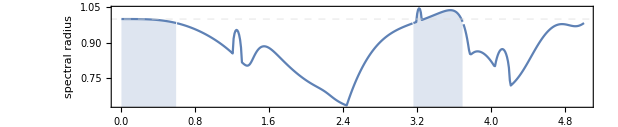

```mathematica
plotspectralradius=ListPlot[listsbigger~Join~listslessorequal,
PlotStyle->RGBColor[0.368417, 0.506779, 0.709798],
Joined->True,
Frame->True,
ImageSize->1000./GoldenRatio,
LabelStyle->15,
FrameLabel->{"Δt ω_0","spectral radius"},
GridLines->{None,{1}},
GridLinesStyle->Directive[Thick,Dashed],
AspectRatio->0.5/(1.+Sqrt[2.]),
FrameTicksStyle->Automatic,
Filling->Thread[Range[Length[listsbigger]]->Axis],
PlotRangePadding->{{Scaled[-0.000000],Scaled[0.0217]},{Automatic,Automatic}}
]
```

```mathematica
diverge=Graphics[{Texture[-Graphics-],Polygon[{{0,0},{0,4.35},{2,4.35},{2,0}},VertexTextureCoordinates->{{0,0},{0,4.35},{2,4.35},{2,0}}]}];
```

```mathematica
plotresponse=ListContourPlot[listallresults,
ColorFunctionScaling->True,
PlotRange->{All,All,{0,20}},
AspectRatio->1./(1.+Sqrt[2.]),PlotLegends->Placed[BarLegend[Automatic,Automatic,LegendLabel->Placed[covariance,Right],LegendMarkerSize->250],Bottom],
ClippingStyle->Texture[-Graphics-],
ColorFunction->"GrayTones",
LabelStyle->15,
ImageSize->1000./GoldenRatio,
FrameLabel->{"Δt ω_0",input},
ImagePadding->{{43,5},{Automatic,3}},
PlotRangePadding->Scaled[.0215],
RegionFunction->Function[{x,y,z},z<10000.],
Prolog->Inset[diverge,{3,0.5},Left,1]
]
```

-Graphics-

### Show plots

```mathematica
plotspectralradius
```

-Graphics-

```mathematica
plotresponse
```

-Graphics-

### Export plots

```mathematica
(*Export["reservoirSpectralRadiusVsResponseA.pdf",plotspectralradius]*)
(*Export["reservoirSpectralRadiusVsResponseB.pdf",plotresponse]*)
```

## 2.3 Input encoding vs response

Here the time between inputs Δt is chosen as to minimize the reservoir spectral radius. Reservoir response is checked for multiple different input encodings.

### Local parameters

The input encodings work as in “Reservoir spectral radius vs response”. In the encoding the quintet corresponds to thermal excitations, magnitude of squeezing, phase of squeezing, magnitude of displacement and phase of displacement. The first number is the factor for the input and the latter number the constant shift. The default settings correspond to setting the magnitude of squeezing to 1 while setting the phase to be 2 π s_k. Order 1 means the output is formed from first moments while order 2 means it’s formed from covariances if displacement is 0 and second moments otherwise.

```mathematica
encodingA={{0.,0.},{0.,0.},{0.,0.},{1.,0.},{0.,0.}};
orderA=1;
```

```mathematica
encodingB={{0.,0.},{1.0,0.},{0.,0.},{0.,0.},{0.,0.}};
orderB=2;
```

```mathematica
encodingC={{0.,0.},{0.,1.},{2.Pi,0.},{0.,0.},{0.,0.}};
orderC=2;
```

```mathematica
encodingD={{0.,0.},{0.,0.},{0.,0.},{0.,1.},{2.Pi,0.}};
orderD=2;
```

### Data generation for magnitude of displacement encoding

#### Additional parameters for QHON generator

```mathematica
encoding=encodingA;
order=orderA;
```

#### Create the QHON instance

```mathematica
(*create a QHON instance (1st moments encoding and readout)*)
{update,getinit,preprocess,readout}=makerandomQHON[n,ancillas,ωbare,g,encoding,order,spat,seed];
```

#### Get the trajectory of states

```mathematica
list1stmom=Rest@FoldList[update,getinit[],preprocess[listinput]];
```

```mathematica
list1stmom//Dimensions
```

{6000,4}

#### Choose a random oscillator and propagate for one more timestep, sample the interval

```mathematica
opts={Frame->True,AspectRatio->1./(1.+Sqrt[2.]),ImageSize->450,LabelStyle->15,DataRange->{0,1}};
```

```mathematica
listαresults=Table[
Table[FoldList[update,Last[list1stmom],preprocess[{in}]][[2,osc]],{in,0.,1.,0.02}],
{osc,1,2n-2Length[ancillas],1}];
```

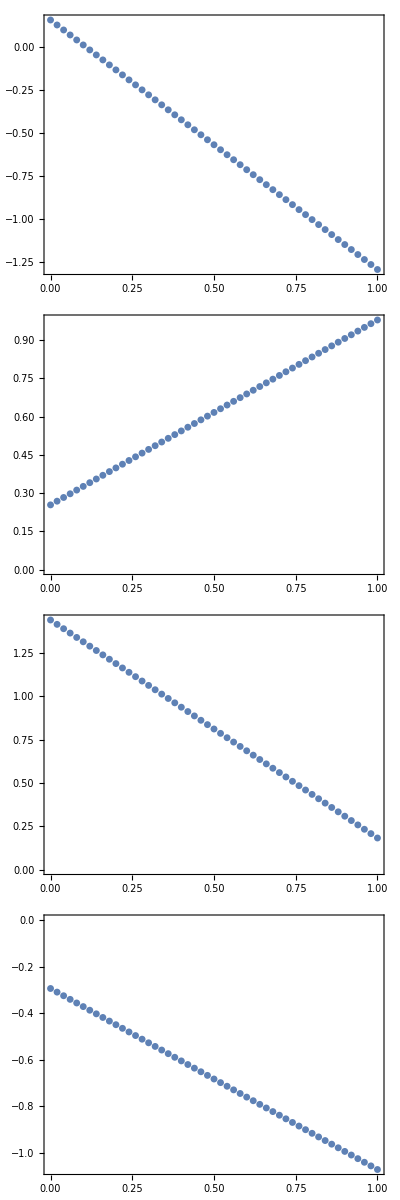

```mathematica
listαresults//Map[ListPlot[#,opts]&]//Column
```

### Data generation for squeezing encoding

#### Additional parameters for QHON generator

```mathematica
encoding=encodingB;
order=orderB;
```

#### Create the QHON instance

```mathematica
(*create a QHON instance (1st moments encoding and readout)*)
{update,getinit,preprocess,readout}=makerandomQHON[n,ancillas,ωbare,g,encoding,order,spat,seed];
```

#### Get the trajectory of states

```mathematica
listcov=Rest@FoldList[update,getinit[],preprocess[listinput]];
```

```mathematica
listcov//Dimensions
```

{6000,4,4}

```mathematica
listcovdiagonal=mydiagonal[listcov]//Dimensions
```

{6000,4}

#### Choose a random oscillator and propagate for one more timestep, sample the interval

```mathematica
opts={Frame->True,AspectRatio->1./(1.+Sqrt[2.]),ImageSize->450,LabelStyle->15,DataRange->{0,1}};
```

```mathematica
listrresults=Table[
Table[FoldList[update,Last[listcov],preprocess[{in}]][[2,osc,osc]],{in,0.,1.,0.02}],
{osc,1,2n-2Length[ancillas],1}];
```

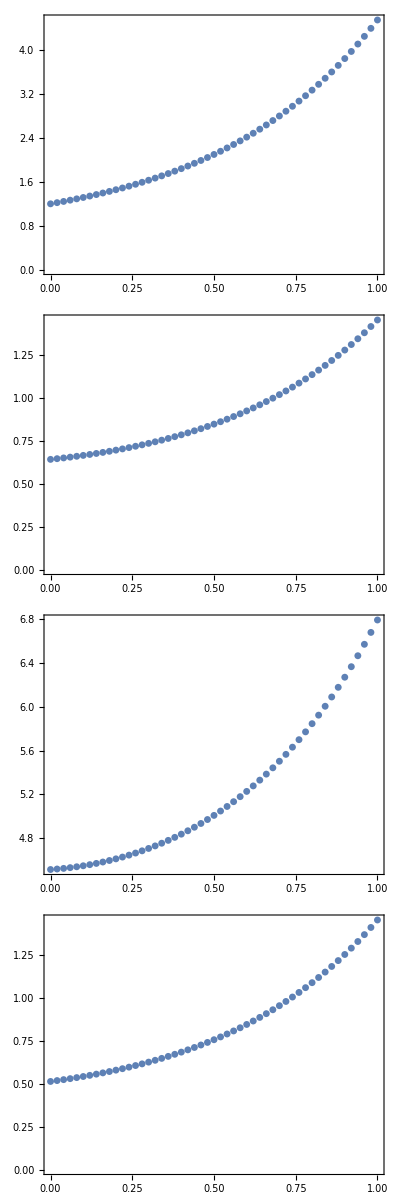

```mathematica
listrresults//Map[ListPlot[#,opts]&]//Column
```

### Data generation for squeezing encoding

#### Additional parameters for QHON generator

```mathematica
encoding=encodingC;
order=orderC;
```

#### Create the QHON instance

```mathematica
(*create a QHON instance (1st moments encoding and readout)*)
{update,getinit,preprocess,readout}=makerandomQHON[n,ancillas,ωbare,g,encoding,order,spat,seed];
```

#### Get the trajectory of states

```mathematica
listcov=Rest@FoldList[update,getinit[],preprocess[listinput]];
```

```mathematica
listcov//Dimensions
```

{6000,4,4}

```mathematica
listcovdiagonal=mydiagonal[listcov]//Dimensions
```

{6000,4}

#### Choose a random oscillator and propagate for one more timestep, sample the interval

```mathematica
opts={Frame->True,AspectRatio->1./(1.+Sqrt[2.]),ImageSize->450,LabelStyle->15,DataRange->{0,1}};
```

```mathematica
listφresults=Table[
Table[FoldList[update,Last[listcov],preprocess[{in}]][[2,osc,osc]],{in,0.,1.,0.02}],
{osc,1,2n-2Length[ancillas],1}];
```

```mathematica
listθresults//Map[ListPlot[#,opts]&]//Column
```

Column[listθresults]

### Data generation for phase of displacement encoding

#### Additional parameters for QHON generator

```mathematica
encoding={{0.,0.},{0.,0.},{0.,0.},{0.,1.},{2.Pi,0.}};
order=2;
```

#### Create the QHON instance

```mathematica
(*create a QHON instance (1st moments encoding and readout)*)
{update,getinit,preprocess,readout}=makerandomQHON[n,ancillas,ωbare,g,encoding,order,spat,seed];
```

#### Get the trajectory of states

```mathematica
list2nd=Rest@FoldList[update,getinit[],preprocess[listinput]];
```

```mathematica
listcov//Dimensions
```

{6000,4,4}

#### Choose a random oscillator and propagate for one more timestep, sample the interval

This is a tad more involved because it’s the readout that combines the covariances and first moments into the second moments

```mathematica
opts={Frame->True,AspectRatio->1./(1.+Sqrt[2.]),ImageSize->450,LabelStyle->15,DataRange->{0,1}};
```

```mathematica
list2ndθresults=Table[
Table[
readout[
{
update[
Last[list2nd],
First@preprocess[{in}]
]
}
][[1,osc]],{in,0.,1.,0.02}],
{osc,1,2n-2Length[ancillas],1}];
```

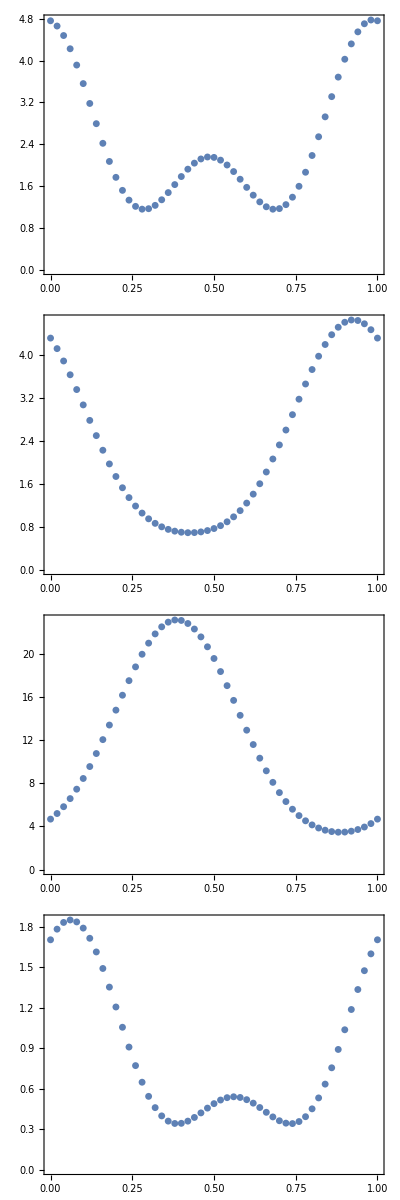

```mathematica
list2ndθresults//Map[ListPlot[#,opts]&]//Column
```

### Make plots

```mathematica
firstmoments=Row[
{
Style["⟨",18],
Style["x̂",Bold,18],
Style["⟩_i",18]
}
]
```

⟨x̂⟩_i

```mathematica
covariances=Row[
{
Style["⟨",18],
Style["x̂",Bold,18],
Style["^2⟩_i-(⟨",18],
Style["x̂",Bold,18],
Style["⟩_i)^2",18]
}
]
```

⟨x̂^2⟩_i-(⟨x̂⟩_i)^2

```mathematica
secondmoments=Row[{Style["⟨",18],Style["x̂",Bold,18],Style["^2⟩_i",18]}]
```

⟨x̂^2⟩_i

```mathematica
input=Style["s_k",18]
```

s_k

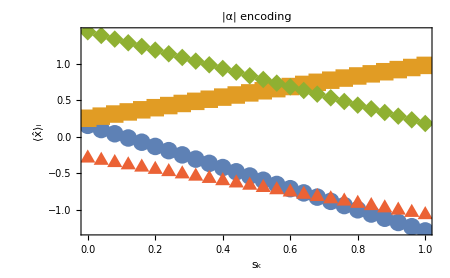

```mathematica
plotα=ListPlot[
listαresults[[All,1;;-1;;2]],
Frame->True,
ImageSize->450,
LabelStyle->15,
DataRange->{0,1},
FrameLabel->{input,firstmoments},
PlotMarkers->{Automatic,18},
PlotLabel->"|α| encoding"
]
```

```mathematica
plotθ=ListPlot[
listθresults[[All,1;;-1;;2]],
Frame->True,
ImageSize->450,
LabelStyle->15,
DataRange->{0,1},
FrameLabel->{input,firstmoments},
PlotMarkers->{Automatic,18},
PlotLabel->"arg(α) encoding"
]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListPlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Symbol[],Frame→True,ImageSize→450,LabelStyle→15,DataRange→{0,1},FrameLabel→{s_k,⟨x̂⟩_i},PlotMarkers→{Automatic,18},PlotLabel→arg(α) encoding]

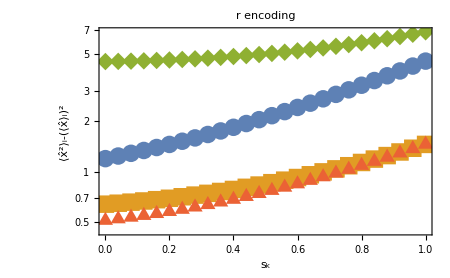

```mathematica
plotr=ListLogPlot[
listrresults[[All,1;;-1;;2]],
Frame->True,
ImageSize->450,
LabelStyle->15,
DataRange->{0,1},
FrameLabel->{input,covariances},
PlotMarkers->{Automatic,18},
PlotLabel->"r encoding"
]
```

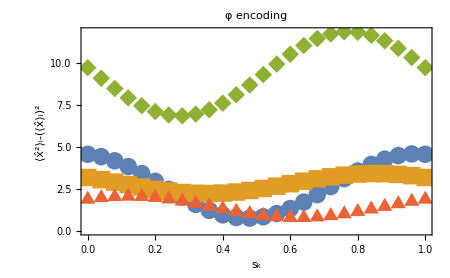

```mathematica
plotφ=ListPlot[
listφresults[[All,1;;-1;;2]],
Frame->True,
ImageSize->450,
LabelStyle->15,
DataRange->{0,1},
FrameLabel->{input,covariances},
PlotMarkers->{Automatic,18},
PlotLabel->"φ encoding"
]
```

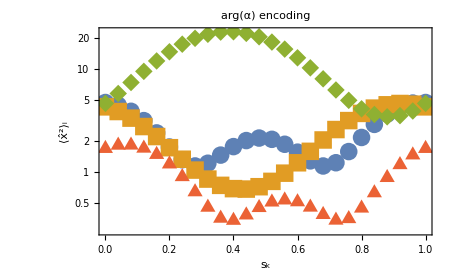

```mathematica
plot2ndθ=ListLogPlot[
list2ndθresults[[All,1;;-1;;2]],
Frame->True,
ImageSize->450,
LabelStyle->15,
DataRange->{0,1},
FrameLabel->{input,secondmoments},
PlotMarkers->{Automatic,18},
PlotLabel->"arg(α) encoding"
]
```

#### Label plots

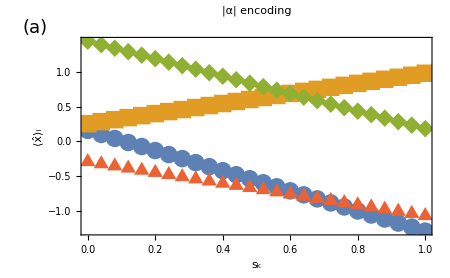

```mathematica
plotαlbl=Show[plotα,Graphics[Text[Style["(a)",18],Scaled@{-0.13,1.05}]],PlotRangeClipping->False,ImagePadding->{{64,Automatic},{Automatic,Automatic}}]
```

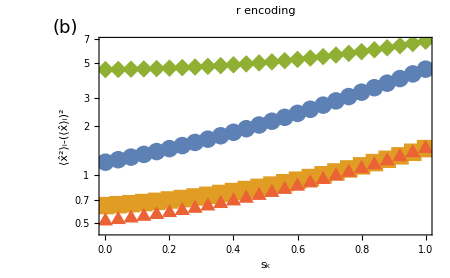

```mathematica
plotrlbl=Show[plotr,Graphics[Text[Style["(b)",18],Scaled@{-0.1,1.05}]],PlotRangeClipping->False,ImagePadding->{{55,Automatic},{Automatic,Automatic}}]
```

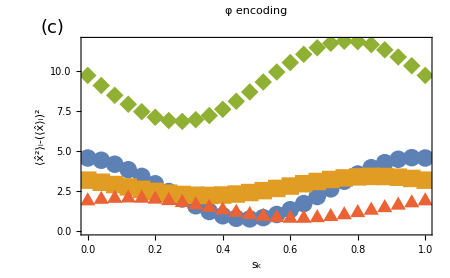

```mathematica
plotφlbl=Show[plotφ,Graphics[Text[Style["(c)",18],Scaled@{-0.08,1.05}]],PlotRangeClipping->False,ImagePadding->{{52,Automatic},{Automatic,Automatic}}]
```

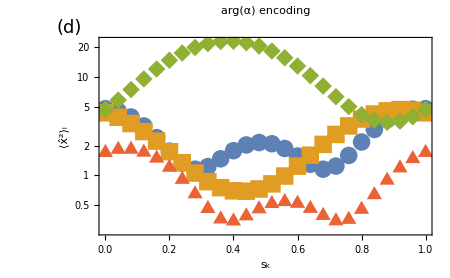

```mathematica
plot2ndθlbl=Show[plot2ndθ,Graphics[Text[Style["(d)",18],Scaled@{-0.09,1.05}]],PlotRangeClipping->False,ImagePadding->{{55,Automatic},{Automatic,Automatic}}]
```

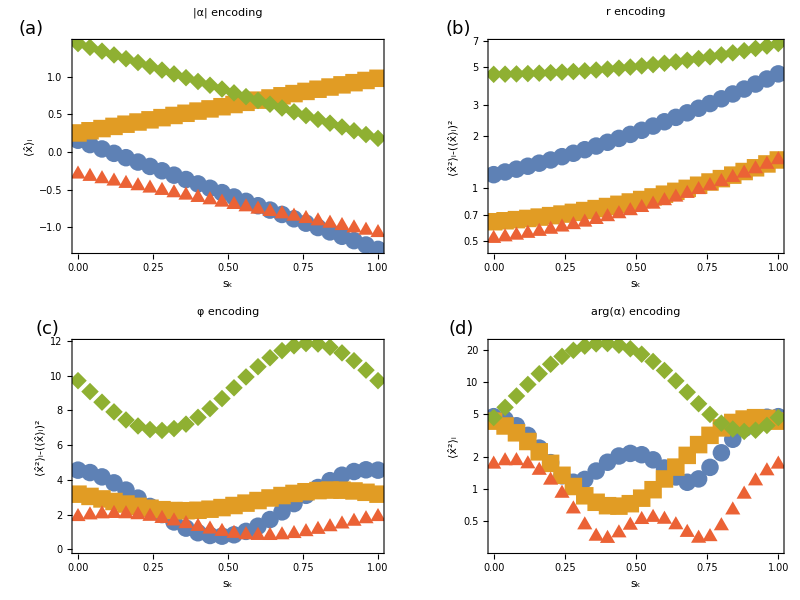

```mathematica
plotcombo=Grid[{{plotαlbl,plotrlbl},{plotφlbl,plot2ndθlbl}}]
```

### Show combo plot

```mathematica
plotcombo
```

-Graphics-

### Export plots

```mathematica
(*Export["figureQHOencodingsHATS.pdf",plotcombo]*)
```